```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sarp/Desktop/Binary_NS_detection_Work

## DATA from A-LIGO BNS Optimized, Einstein Telescope B Low-frequency end

#### ASD = 2 h̃(f) √f where h̃(f) is the Fourier transform of h(t)

```mathematica
ALIGO2017Data={{7*10^5,6000,100,20,4,2,1,0.9,0.8,0.9,1,2,4}*10^-23,{9,10,15,20,30,40,70,80,100,200,400,1000,1200}};
ALIGODesigndata={{10^5,10^4,100,32,20,8,5,2.35,1,0.6,0.4,0.3,0.25,0.3,0.8,3}*10^-23,{6,7,9,9.7,10,11.89,14,20,30,40,60,200,300,400,900,1200}};
ETdata={{10^6,500,50,40,20,14,6,3,2,1,0.5,0.15,0.06,0.03,0.025,0.03,0.07}*10^-23,{0.5,1,1.2,1.3,1.5,2,3,4,5,7,10,20,30,60,150,300,1000}};
data={ALIGO2017Data,ALIGODesigndata,ETdata};
choice=3;
Ls=Table[Length[data[[i,1]]],{i,1,3}]
```

{13,16,17}

```mathematica
ThreeIFOData=Table[{data[[j,2,i]],data[[j,1,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
GWFreqs=Table[ThreeIFOData[[j,i,1]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDData=Table[ThreeIFOData[[j,i,2]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDvFreqData=Table[{GWFreqs[[j,i]],ASDData[[j,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

## Preliminaries

```mathematica
Clear[x,h]
```

```mathematica
X=(G M Ω/c^3)^(2/3);
Msun=1.989*10^30;
clight=299792458;
Ggrav=6.67*10^-11;
ν=1/4;
Mc=ν^(3/5)M;
fISCO=c^3/(6^(3/2)π G M);
A=π^(-2/3)√(5/12);
AngAveFact=1/Pi Integrate[(1+Cos[i]^2)/2,{i,0,Pi}];
InclinationAv=2Pi 1/(4Pi)Integrate[(((1+Cos[i]^2)/2)^2+Cos[i]^2)Sin[i],{i,0,-Pi,Pi}]
Mpc=10^6*360/(2π)*3600*149597870700.;
GWfreqIsco=fISCO/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
fISCO/.G->6.67*10^-11/.M->(2.74Msun)/.c->clight
```

4/5

1605.37

#### Frequency and Time Domain Strains generated by BNS

```mathematica
h̃=AngAveFact A c/LumDist(G Mc/c^3)^(5/6)GWFreqs^(-7/6)  ;(* strain in FD, Colpi-Sesana Eqs.(29-30) *)

h=AngAveFact 4/LumDist(G Mc/c^2)^(5/3)(π GWFreqs/c)^(2/3);(* strain in TD Colpi-Sesana Eqs.(29-30) *)
(h̃)/Mpc/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
h/Mpc/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
```

```mathematica
hFD[f_,D_]=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},AngAveFact A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
hTD[f_,D_]=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},AngAveFact 4/D(G Mc/c^2)^(5/3)(π f/c)^(2/3)]
```

3012.04/(D f^(7/6))

(3.82305 f^(2/3))/D

## AVERAGING of the ANTENNA PATTERN

```mathematica
Fplus=1/2(1+Cos[θ]^2)Cos[2ϕ]Cos[2ψ]-Cos[θ]Sin[2ϕ]Sin[2ψ];
Fx=1/2(1+Cos[θ]^2)Cos[2ϕ]Sin[2ψ]+Cos[θ]Sin[2ϕ]Cos[2ψ];
```

```mathematica
Integrate[Fplus*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,π}]
```

0

```mathematica
Integrate[Fplus*Sin[θ],{θ,0,Pi}]
```

4/3 Cos[2 ϕ] Cos[2 ψ]

```mathematica
1/(8 Pi^2)Integrate[Fplus^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
1/(8 Pi^2)Integrate[Fx^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
```

1/5

1/5

## Scaling of Important Quantities in Terms of m_1, m_2

```mathematica
(* Mass ranges *)
R1={1,2}/Rationalize[1.4]
R2=R1;
```

{5/7,10/7}

```mathematica
Mchirp[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5);
ReducedMass[m1_,m2_]:=(m1 m2)/(m1+m2);
```

```mathematica
freq[m1_,m2_]:=(m1+m2)^(1/2);
fdot[m1_,m2_]:=Mchirp[m1,m2]^(5/3) freq[m1,m2]^(11/3);
Edot[m1_,m2_]:=ReducedMass[m1,m2]^2(m1+m2)^3;
FDstrain[m1_,m2_]:=Mchirp[m1,m2]^(5/6)(*freq[m1,m2]^(-7/6)*);
InspiralTime[m1_,m2_]:=1/(m1 m2 (m1+m2));
MergerFreq[m1_,m2_]:=1/(m1+m2);
```

```mathematica
Simplify[Edot[m1,m2],m1+m2>0]
Simplify[fdot[m1,m2],m1+m2>0]
InspiralTime[m1,m2]
Simplify[FDstrain[m1,m2],m1+m2>0]
```

m1^2 m2^2 (m1+m2)

m1 m2 (m1+m2)^(3/2)

1/(m1 m2 (m1+m2))

(√(m1 m2))/(m1+m2)^(1/6)

```mathematica
N[{Min[freq[R1,R2]],freq[1,1],Max[freq[R1,R2]]},3]
N[{Min[Edot[R1,R2]],Edot[1,1],Max[Edot[R1,R2]]},3]
N[{Min[fdot[R1,R2]],fdot[1,1],Max[fdot[R1,R2]]},3]
N[{Min[InspiralTime[R1,R2]],InspiralTime[1,1],Max[InspiralTime[R1,R2]]},3]
N[{Min[FDstrain[R1,R2]],FDstrain[1,1],Max[FDstrain[R1,R2]]},3]
N[{Min[MergerFreq[R1,R2]],MergerFreq[1,1],Max[MergerFreq[R1,R2]]},3]
N[{Min[InspiralTime[{1.2,1.6}/1.4,{1.2,1.6}/1.4]],InspiralTime[1,1],Max[InspiralTime[{1.2,1.6}/1.4,{1.2,1.6}/1.4]]},3]
N[{Min[FDstrain[{1.2,1.6}/1.4,{1.2,1.6}/1.4]],FDstrain[1,1],Max[FDstrain[{1.2,1.6}/1.4,{1.2,1.6}/1.4]]},3]
N[{Min[MergerFreq[{1.2,1.6}/1.4,{1.2,1.6}/1.4]],MergerFreq[1,1],Max[MergerFreq[{1.2,1.6}/1.4,{1.2,1.6}/1.4]]},6]
```

{1.2,1.41,1.69}

{0.372,2.,11.9}

{0.871,2.83,9.86}

{0.172,0.5,1.37}

{0.673,0.891,1.2}

{0.35,0.5,0.7}

{0.334961,0.5,0.793981}

{0.783501,0.891,0.995761}

{0.4375,0.5,0.583333}

## QUASI-CIRCULAR APPROXIMATION

```mathematica
Block[{M=2.8Msun},NSolve[96/5(Ggrav Mc)^(5/3)/clight^5 Ω^(5/3)==0.01,Ω]]
%[[1,1,2]]/Pi
```

{{Ω→1785.66}}

568.393

```mathematica
Block[{M=2.8Msun},NSolve[96/5(Ggrav Mc)^(5/3)/clight^5 Ω^(5/3)==0.001,Ω]]
%[[1,1,2]]/Pi
```

{{Ω→448.537}}

142.774

```mathematica
Block[{M=2.8Msun,Ω=Pi*200},96/5(Ggrav Mc)^(5/3)/clight^5 Ω^(5/3)]
```

0.00175375

## OCTUPOLE and CURRENT QUADRUPOLE

```mathematica
(*Kepler's law *)
```

```mathematica
ΩK=(√G √M)/r^(3/2);
```

```mathematica
v=r ΩK
```

(√G √M)/(√r)

```mathematica
Solve[Ω==ΩK,r][[1,1,2]]
```

1/(Ω/(√G √M))^(2/3)

```mathematica
Simplify[v^2/c^2/.r->Solve[Ω==ΩK,r][[1,1,2]]/.Ω->π f,G>0&&M>0]
%/.G->Ggrav/.c->clight/.M->2.8 Msun
v2c2=%/.f->100
Print["Mass octupole to quadrupole ratio at 100 Hz: ",25/896 v2c2,"\nMass octupole to current quadrupole ratio at 100 Hz: ",1215/896 v2c2]
1215/25.
```

((f G M)^(2/3) π^(2/3))/c^2

0.00123331 f^(2/3)

0.0265708

Mass octupole to quadrupole ratio at 100 Hz: 0.000741372
Mass octupole to current quadrupole ratio at 100 Hz: 0.0360307

48.6

## NEGLECTING NS SPIN

```mathematica
χ=Block[{M=1.4Msun,R=11000,Ii=2/5 M R^2},clight/Ggrav Ii/(1.4Msun)^2(2π)/10^-2]
```

0.049086

```mathematica
ScientificForm[4 Ggrav (100π)1.4 Msun χ/clight^3]
```

4.252×10^-4

## COSMOLOGY

```mathematica
z=0.25;
1571/(1+z)
```

1256.8

```mathematica
(1+z)^(5/3)
(1+z)^(5/6)
```

1.4505

1.20437

## DETECTORS and SOURCES

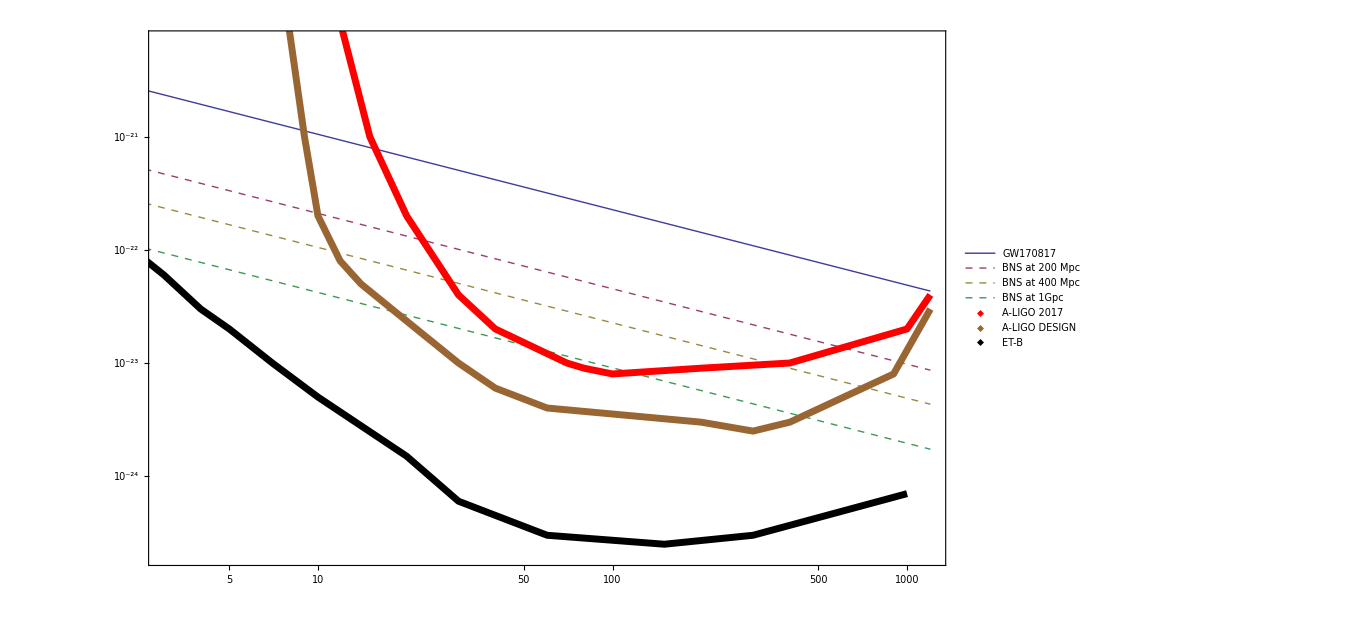

```mathematica
ASDPlots=Show[LogLogPlot[{2 √f hFD[f,40Mpc],2 √f hFD[f,200Mpc],2 √f hFD[f,400Mpc],2 √f hFD[f,1000Mpc]},{f,1,1200},PlotStyle->{Automatic,Dashed,Dashed,Dashed},PlotRange->{{1,1200},{2 10^-25,7 10^-21}},PlotLegends->{"GW170817","BNS at 200 Mpc","BNS at 400 Mpc","BNS at 1Gpc"}],ListLogLogPlot[{ASDvFreqData[[1]],ASDvFreqData[[2]],ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thickness[0.005],Red},{Thickness[0.005],Brown},{Thickness[0.005],Black}},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO 2017","A-LIGO DESIGN","ET-B"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->1000,Frame->True]
```

```mathematica
Export["Figures/ASDPlots.pdf",ASDPlots]
```

Figures/ASDPlots.pdf

## Inspiral time, accumulated phase: 0PN to 2PN expressions

```mathematica
Tinsp0PN[fin_]:=5/(256 π^(8/3))1/ν(c^3/(G M))^(5/3)fin^(-8/3)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
Phi0PN[fin_]:=2(5G Mc/c^3)^(-5/8)Tinsp0PN[fin]^(5/8)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
Ncycles0PN[fin_]:=1/(32 π^(8/3))(G Mc/c^3)^(-5/3)(fin^(-5/3)-fISCO^(-5/3))/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
```

```mathematica
10^(-5/3)/1000.^(-5/3)
```

2154.43

### 2PN expressions from Section 5.6.4 of Maggiore’s Book

```mathematica
τ0[f_]:=5/(256 ν f π)(π G M/c^3 f)^(-5/3)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
τ1[f_]:=5/(192 ν f π)(π G M/c^3 f)^-1(743/336+11/4 ν)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
τ15[f_]:=1/(8 ν f)(π G M/c^3 f)^(-2/3)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
τ2[f_]:=5/(128 ν f π)(π G M/c^3 f)^(-1/3)(3058673/1016064+5429/1008 ν+617/144 ν^2)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
```

```mathematica
Tinsp2PN[f_,fin_]:=τ0[fin](1-(f/fin)^(-8/3))+τ1[fin](1-(f/fin)^-2)-τ15[fin](1-(f/fin)^(-5/3))+τ2[fin](1-(f/fin)^(-4/3));
Phi2PN[f_,fin_]:=16 π/5 fin(τ0[fin] (1-(f/fin)^(-5/3))+5/4 τ1[fin](1-(f/fin)^-1)-25/16 τ15[fin](1-(f/fin)^(-2/3))+5/2 τ2[fin](1-(f/fin)^(-1/3)));
```

## Definining the SNR

```mathematica
Snoise=Table[Interpolation[ASDvFreqData[[i]],InterpolationOrder->1],{i,1,Length[data]}];
SNR[i_,fi_,ff_,D_]:=NIntegrate[4 hFD[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}]^(1/2)
```

## CHECKS: GW170817 at A-LIGO 2017 Swept from 30 Hz to ~ 2000 Hz in 60 seconds and ~ 3000 cycles with SNR = 32.4

```mathematica
fin=30;
fout=300;
SNR300Hz=SNR[1,fin,fout,40Mpc];
SNR1200Hz=SNR[1,fin,GWfreqIsco,40Mpc];
Print["SNR(40 -> 300Hz) = ", SNR300Hz]
Print["SNR(40 -> f_ISCO) = ", SNR1200Hz]
Print["Inspiral time = ", Tinsp0PN[fin] ,"(0 PN) + ",Tinsp2PN[GWfreqIsco,fin]-Tinsp0PN[fin], "(2PN) = ",Tinsp2PN[GWfreqIsco,fin]," seconds"]
Print["𝒩_cycles = ", Ncycles0PN[fin],"(0 PN) + ",Phi2PN[GWfreqIsco,fin]/(2π)-Ncycles0PN[fin], "(2PN) = ",Phi2PN[GWfreqIsco,fin]/(2π)]
```

SNR(40 -> 300Hz) = 32.7054

SNR(40 -> f_ISCO) = 33.5743

Inspiral time = 53.5763(0 PN) + 1.13559(2PN) = 54.7119 seconds

𝒩_cycles = 2568.15(0 PN) + 53.8213(2PN) = 2621.98

```mathematica
GWfreqIsco
```

1570.97

## GW170817, BNS(200Mpc) at A-LIGO-DESIGN

### Picking out the LIGO-band entrance frequencies

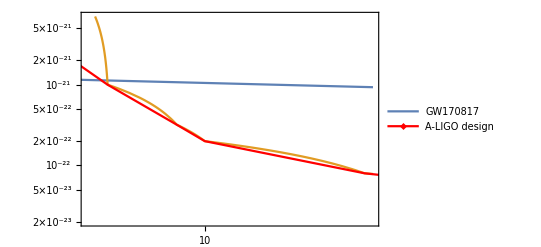

```mathematica
Show[LogLogPlot[{2 √f hFD[f,40Mpc],Snoise[[2]][f]},{f,7,12},PlotStyle->{Automatic},PlotRange->{{8.8,12},{2 10^-23,7 10^-21}},PlotLegends->{"GW170817"}],ListLogLogPlot[{ASDvFreqData[[2]]},Joined->True,PlotStyle->{{Thick,Red},Brown,Black},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

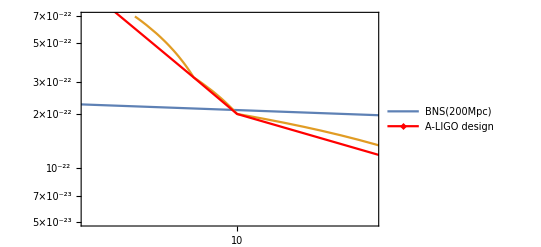

```mathematica
Show[LogLogPlot[{2 √f hFD[f,200Mpc],Snoise[[2]][f]},{f,8,15},PlotStyle->{Automatic},PlotRange->{{9,11},{5 10^-23,7 10^-22}},PlotLegends->{"BNS(200Mpc)"}],ListLogLogPlot[{ASDvFreqData[[2]]},Joined->True,PlotStyle->{{Thick,Red},Brown,Black},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

### Threshold SNR frequencies

```mathematica
fi={9,10}; (*Entry frequencies *)
dL={40Mpc, 200Mpc};
```

```mathematica
{SNR[2,fi[[1]],16.735,dL[[1]]],SNR[2,fi[[1]],20.75,dL[[1]]],SNR[2,fi[[1]],24.91,dL[[1]]]}
Freqs40Mpc2020={16.775,20.75,24.91};
```

{10.0074,15.027,20.0195}

```mathematica
Block[{i=2},{SNR[2,fi[[i]],47.4,dL[[i]]],SNR[2,fi[[i]],84.725,dL[[i]]]}]
Freq200Mpc2020={47.4,85.};
```

{10.0005,15.0003}

```mathematica
SNR40Mpc2020=SNR[2,fi[[1]],GWfreqIsco,dL[[1]]]
SNR200Mpc2020=SNR[2,fi[[2]],GWfreqIsco,dL[[2]]]
```

98.4994

19.6991

### ADVANCE WARNING TIMES

```mathematica
Print["GW170817 at A-LIGO-Design:"]
Print["---------------------------"]
Print["Total SNR(",fi[[1]],"Hz -> f_ISCO) = ", SNR40Mpc2020]
Print["Warning times with SNR thresholds of {10,15,20}  = ", Table[Tinsp2PN[GWfreqIsco,Freqs40Mpc2020[[i]]],{i,1,Length[Freqs40Mpc2020]}]," seconds"]
(*Print["Total inspiral time = ",Tinsp2PN[GWfreqIsco,fi[[1]]], " seconds"]*)
Print["******************************************************************************************"]
Print["BNS{200Mpc) at A-LIGO-Design:"]
Print["------------------------------"]
Print["Total SNR(",fi[[2]],"Hz -> f_ISCO) = ", SNR200Mpc2020]
Print["Warning times with SNR thresholds of {10,15} = ",Table[ Tinsp2PN[GWfreqIsco,Freq200Mpc2020[[i]]],{i,1,Length[Freq200Mpc2020]}]," seconds"]
(*Print["Total inspiral time = ",Tinsp2PN[GWfreqIsco,fi[[2]]], " seconds"]*)
```

GW170817 at A-LIGO-Design:

---------------------------

Total SNR(9Hz -> f_ISCO) = 98.4994

Warning times with SNR thresholds of {10,15,20}  = {256.812,145.871,89.7204} seconds

******************************************************************************************

BNS{200Mpc) at A-LIGO-Design:

------------------------------

Total SNR(10Hz -> f_ISCO) = 19.6991

Warning times with SNR thresholds of {10,15} = {16.1926,3.41029} seconds

## GW170817, BNS(400Mpc), BNS(1Gpc) at EINSTEIN TELESCOPE B

### Picking out the LIGO-band entrance frequencies

InterpolatingFunction::dmval: Input value {0.200038} lies outside the range of data in the interpolating function. Extrapolation will be used.

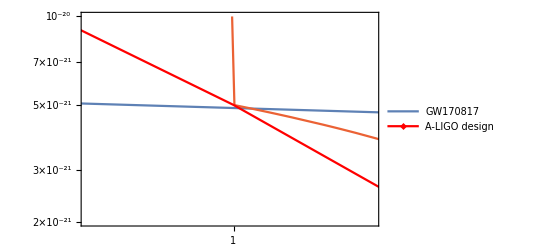

```mathematica
Show[LogLogPlot[{2 √f hFD[f,40Mpc],2 √f hFD[f,400Mpc],2 √f hFD[f,1000Mpc],Snoise[[3]][f]},{f,0.2,2000},PlotStyle->{Automatic},PlotRange->{{0.95,1.05},{2 10^-21,10^-20}},PlotLegends->{"GW170817"}],ListLogLogPlot[{ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thick,Red},Brown,Black},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

InterpolatingFunction::dmval: Input value {0.200038} lies outside the range of data in the interpolating function. Extrapolation will be used.

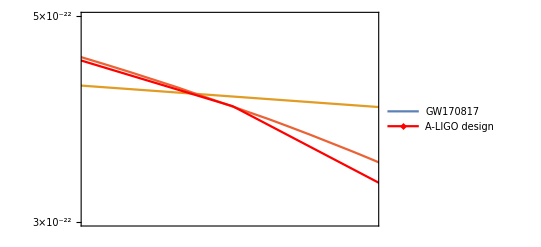

```mathematica
Show[LogLogPlot[{2 √f hFD[f,40Mpc],2 √f hFD[f,400Mpc],2 √f hFD[f,1000Mpc],Snoise[[3]][f]},{f,0.2,2000},PlotStyle->{Automatic},PlotRange->{{1.25,1.35},{3 10^-22,5 10^-22}},PlotLegends->{"GW170817"}],ListLogLogPlot[{ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thick,Red},Brown,Black},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

InterpolatingFunction::dmval: Input value {0.200038} lies outside the range of data in the interpolating function. Extrapolation will be used.

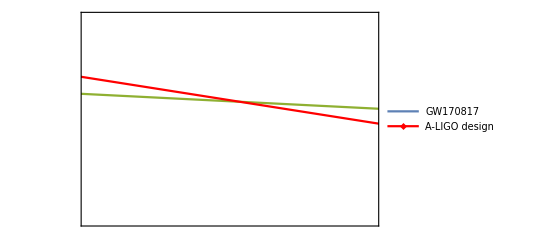

```mathematica
Show[LogLogPlot[{2 √f hFD[f,40Mpc],2 √f hFD[f,400Mpc],2 √f hFD[f,1000Mpc],Snoise[[3]][f]},{f,0.2,2000},PlotStyle->{Automatic},PlotRange->{{2.18,2.2},{1.1 10^-22,1.2 10^-22}},PlotLegends->{"GW170817"}],ListLogLogPlot[{ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thick,Red},Brown,Black},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

### Threshold SNR frequencies

```mathematica
fi={1,1.29,2.19}; (*Entry frequencies *)
dL={40Mpc, 400Mpc,1000Mpc};
```

```mathematica
{SNR[3,fi[[1]],1.8,dL[[1]]],SNR[3,fi[[1]],2.32,dL[[1]]],SNR[3,fi[[1]],2.9,dL[[1]]]};
Freqs40MpcET={1.8,2.32,2.9};
```

```mathematica
Block[{i=2},{SNR[3,fi[[i]],8.6,dL[[i]]],SNR[3,fi[[i]],11.83,dL[[i]]],SNR[3,fi[[i]],16.22,dL[[i]]]}];
Freqs400MpcET={8.6,11.83,16.22};
```

```mathematica
Block[{i=3},{SNR[3,fi[[i]],19.9,dL[[i]]],SNR[3,fi[[i]],27.,dL[[i]]],SNR[3,fi[[i]],32.4,dL[[i]]]}];
Freqs1GpcET={19.9,27,32.4};
```

```mathematica
SNR40MpcET=SNR[3,fi[[1]],GWfreqIsco,dL[[1]]];
SNR400MpcET=SNR[3,fi[[2]],GWfreqIsco,dL[[2]]];
SNR1GpcET=SNR[3,fi[[3]],GWfreqIsco,dL[[3]]];
```

### ADVANCE WARNING TIMES

```mathematica
Twarn40MpcET=Table[Tinsp2PN[GWfreqIsco,Freqs40MpcET[[i]]],{i,1,Length[Freqs40MpcET]}];
Twarn400MpcET=Table[Tinsp2PN[GWfreqIsco,Freqs400MpcET[[i]]],{i,1,Length[Freqs400MpcET]}];
Twarn1GpcET=Table[Tinsp2PN[GWfreqIsco,Freqs1GpcET[[i]]],{i,1,Length[Freqs1GpcET]}];
```

```mathematica
Print["GW170817 at ET:"]
Print["---------------------------"]
Print["Total SNR(",fi[[1]]," -> f_ISCO) = ", SNR40MpcET]
Print["Warning times with SNR thresholds of {10,15,20}  = ",Twarn40MpcET ," seconds"]
Print["                                                   = ",Twarn40MpcET/3600 ," hours"]
(*Print["Total inspiral time = ",Tinsp2PN[GWfreqIsco,fi[[1]]]/86400," days"]*)
(*Print["𝒩_cycles = ",Phi2PN[GWfreqIsco,fi[[1]]]/(2π)]*)
Print["******************************************************************************************"]
Print["BNS{400Mpc) at ET:"]
Print["------------------------------"]
Print["Total SNR(",fi[[2]]," -> f_ISCO) = ", SNR400MpcET]
Print["Warning time with SNR thresholds of {10,15,20} = ",Table[ Tinsp2PN[GWfreqIsco,Freqs400MpcET[[i]]],{i,1,Length[Freqs400MpcET]}]," seconds"]
Print["                                                 = ",Twarn400MpcET/60 ," minutes"]
(*Print["Total inspiral time = ",Tinsp2PN[GWfreqIsco,fi[[2]]]/86400," days"]*)
Print["******************************************************************************************"]
Print["BNS{1Gpc) at ET:"]
Print["------------------------------"]
Print["Total SNR(",fi[[3]]," -> f_ISCO) = ", SNR1GpcET]
Print["Warning time with SNR thresholds of {10,15,20} = ",Table[ Tinsp2PN[GWfreqIsco,Freqs1GpcET[[i]]],{i,1,Length[Freqs1GpcET]}]," seconds"]
(*Print["Total inspiral time = ",Tinsp2PN[GWfreqIsco,fi[[3]]]/86400," days"]*)
```

GW170817 at ET:

---------------------------

Total SNR(1 -> f_ISCO) = 1281.44

Warning times with SNR thresholds of {10,15,20}  = {97639.5,49669.4,27417.5} seconds

= {27.1221,13.7971,7.61599} hours

******************************************************************************************

BNS{400Mpc) at ET:

------------------------------

Total SNR(1.29 -> f_ISCO) = 128.144

Warning time with SNR thresholds of {10,15,20} = {1518.72,650.221,280.853} seconds

= {25.3119,10.837,4.68088} minutes

******************************************************************************************

BNS{1Gpc) at ET:

------------------------------

Total SNR(2.19 -> f_ISCO) = 51.2545

Warning time with SNR thresholds of {10,15,20} = {163.037,72.4125,44.5812} seconds

## Peters and Matthews Timescales

```mathematica
pdot[e_,p_]:=-64/5(1-e^2)^(3/2)p^-3
edot[e_,p_]:=-304/15 e (1-e^2)^(3/2)p^-4
```

```mathematica
TpTeRatio=19/12(1+7/8 e^2)^-1(1+121/304 e^2);
```

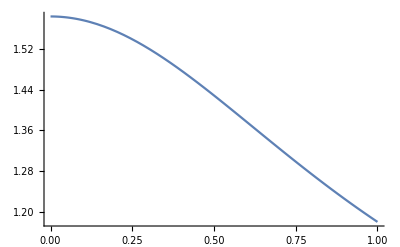

```mathematica
Plot[TpTeRatio,{e,0,1}]
```

```mathematica
6*(100./1570)^(-2/3)
```

37.6199

```mathematica
1/%
```

0.0265817

```mathematica
6*(200./1570)^(-2/3)
1/%
```

23.6991

0.0421958

```mathematica
37.61990420422838*2.8Msun G/1000/c^2/.c->clight/.G->6.67 10^-11
```

155.487

```mathematica
100(%/1000)^(3/2)
```

6.13116

```mathematica
6*(1./GWfreqIsco)^(-2/3)
```

810.829

```mathematica
(1000/%)^(-3/2)
```

0.730119

```mathematica
g[e_]:=e^(12/19)/(1-e^2)(1+121/304 e^2)^(870/2299);
```

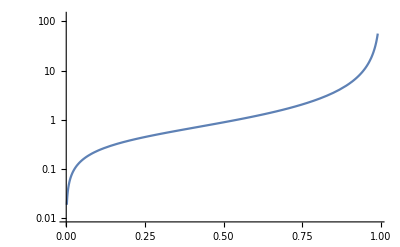

```mathematica
LogPlot[g[e],{e,0,0.99}]
```

```mathematica
(810.8285990700242/(2 10^9)g[0.617])^(19/12)
```

1.08555×10^-10

```mathematica
810.8285990700242/(2 10^9)g[0.617]
```

5.0901×10^-7

```mathematica
g[1.08555 10^-10]
```

5.0901×10^-7

## Post-Newtonian Details from Blanchet’s Review Article

```mathematica
(* 3.5 PN non-spinning binary phase *)
phi[x_,x0_]=-x^(-5/2)/(32ν)(1+(3715/1008+55/12 ν)x-10 π x^(3/2)+(15293365/1016064+27145/1008 ν+3085/144 ν^2)x^2+(38645/1344-65/16 ν)π x^(5/2)Log[x/x0]+(12348611926451/18776862720-160/3 π^2-1712/21 EulerGamma-856/21 Log[16x]+(-15737765635/12192768+2255/48 π^2)ν+76055/6912 ν^2-127825/5184 ν^3)x^3+(77096675/2032128+378515/12096 ν-74045/6048 ν^2)π x^(7/2));
```

```mathematica
K=SeriesCoefficient[X/.Ω-> π f,{f,0,2/3}];
Xvar=K f^(2/3);
Clear[T]
Θ=ν c^3/(G M)(Δt);
xoft[T_]=(1/4)T^(-1/4)(1+(743/4032+11/48 ν)T^(-1/4)-1/5 π T^(-3/8)+(19583/254016+24401/193536 ν+31/288 ν^2)T^(-1/2)+(-11891/53760+109/1920 ν)π T^(-5/8)+(-10052469856691/6008596070400+1/6 π^2+107/420 EulerGamma-107/3360 Log[T/256]+(3147553127/780337152-451/3072 π^2)ν-15211/442368 ν^2+25565/331776 ν^3)T^(-3/4)+(-113868647/433520640-31821/143360 ν+294941/3870720 ν^2)π T^(-7/8));
```

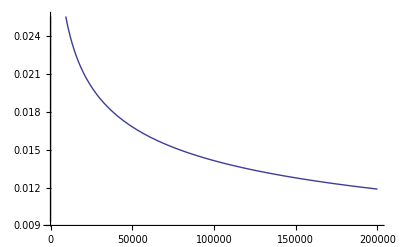

```mathematica
Plot[{xoft[t],xStart,xEnd},{t,1,200000}]
```

```mathematica
phi[xend,xStart]
```

-1/(8 xend^(5/2))(1+(2435 xend)/504-10 π xend^(3/2)+(11747195 xend^2)/508032+(357185 π xend^(7/2))/7938+xend^3 (12354290668751/18776862720-(1712 EulerGamma)/21-(160 π^2)/3+1/4 (-15737765635/12192768+(2255 π^2)/48)-856/21 Log[16 xend])+1165/42 π xend^(5/2) Log[xend/xStart])

```mathematica
xTime=xoft[Θ]/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight
```

1/Δt^(1/4)0.0215436 (1-0.000184953/Δt^(7/8)-0.00141761/Δt^(5/8)+0.000856529/(√Δt)-0.0158946/Δt^(3/8)+0.020817/Δt^(1/4)+(0.000639937 (-10058148598991/6008596070400+(107 EulerGamma)/420+π^2/6+1/4 (3147553127/780337152-(451 π^2)/3072)-(107 Log[70.8343 Δt])/3360))/Δt^(3/4))

```mathematica
xStart=Xvar/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight/.f->30
```

0.0119074

```mathematica
xEnd=Xvar/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight/.f->400
```

0.0669542

```mathematica
xend=Xvar/.f->(fISCO)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight
```

0.166667

```mathematica
xTime/.Δt->1
```

0.0216423

```mathematica
Tstart=NSolve[xoft[T]-xStart==0,T,Reals]//Quiet
Tend=NSolve[xoft[T]-xEnd==0,T,Reals]//Quiet
```

{{T→1.02097},{T→198177.}}

{{T→1.63633},{T→167.16}}

```mathematica
NSolve[198177-Θ/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight,Δt]
```

{{Δt→10.9287}}

```mathematica
Θ/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight/.Δt->60
```

1.08801×10^6

```mathematica
xBNS=X/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight/.Ω->(π fGW)
```

0.00123331 fGW^(2/3)

```mathematica
X0s=(NSolve[phi[xBNS,x0]==0,x0]/.fGW->Freqs2017)[[1,1,2]]
```

0.00123331 2.71828^(214831./Freqs2017^(5/3)+1280.08/Freqs2017-292.316/Freqs2017^(2/3)+7.55581/Freqs2017^(1/3)+0.0152161 Freqs2017^(1/3)+0.00200067 Freqs2017^(2/3)) Freqs2017^(0.666667-0.0109515 Freqs2017^(1/3))

```mathematica
AccumPhase=Table[phi[xBNS/.fGW->GWfreqIsco,X0s[[i]]],{i,1,Length[Freqs2017]}];
Ncycles=AccumPhase/π
```

{}

```mathematica
(NSolve[phi[xBNS,x0]==0,x0]/.fGW->30)[[1,1,2]]
```

4.05684160394499×10^326

```mathematica
phi[xBNS/.fGW->GWfreqIsco,%]
```

8213.23

```mathematica
%/π
```

2614.35

```mathematica
Freqs2017
```

Freqs2017

## Colpi-Sesana Leading-order Formulation

#### Luminosity distance RE-calculation

```mathematica
(* Using C-S formulae along with h̃=ASD/2 √f *)
```

```mathematica
eqs=Table[(ASDdata/(2 √GWfreqData)-A c/dL(G Mc/c^3)^(5/6)GWfreqData^(-7/6)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight)[[i]],{i,1,Length[GWfreqData]}];
Table[(NSolve[eqs[[i]]==0,dL][[1,1,2]])/Mpc,{i,1,Length[GWfreqData]}]
```

{}

```mathematica
Tinsp=5/(256 π^(8/3))1/ν(c^3/(G M))^(5/3)GWfreqData^(-8/3)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight
```

465546./GWfreqData^(8/3)

```mathematica
NcyclesNewt=1/(32 π^(8/3))(G Mc/c^3)^(-5/3)(GWfreqData^(-5/3)-fISCO^(-5/3))/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight
```

744874. (-4.71037×10^-6+1/GWfreqData^(5/3))

```mathematica
PhiN=2(5G Mc/c^3)^(-5/8)Tinsp^(5/8)/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight
```

4.68018×10^6 (1/GWfreqData^(8/3))^(5/8)

```mathematica
phi[x_,x0_]=-x^(-5/2)/(32ν)(1+(3715/1008+55/12 ν)x-10 π x^(3/2)+(15293365/1016064+27145/1008 ν+3085/144 ν^2)x^2+(38645/1344-65/16 ν)π x^(5/2)Log[x/x0]+(12348611926451/18776862720-160/3 π^2-1712/21 EulerGamma-856/21 Log[16x]+(-15737765635/12192768+2255/48 π^2)ν+76055/6912 ν^2-127825/5184 ν^3)x^3+(77096675/2032128+378515/12096 ν-74045/6048 ν^2)π x^(7/2));
```

```mathematica
xBNS=X/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight/.Ω->(π fGW)
```

0.00123331 fGW^(2/3)

```mathematica
fBNS=fISCO/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight
```

1570.97

```mathematica
fISCO
```

c^3/(6 √6 G M π)

```mathematica
GWfreqIsco
```

1570.97

```mathematica
X0s=(NSolve[phi[xBNS,x0]==0,x0]/.fGW->GWfreqData)[[1,1,2]]
```

0.00123331 2.71828^(214831./GWfreqData^(5/3)+1280.08/GWfreqData-292.316/GWfreqData^(2/3)+7.55581/GWfreqData^(1/3)+0.0152161 GWfreqData^(1/3)+0.00200067 GWfreqData^(2/3)) GWfreqData^(0.666667-0.0109515 GWfreqData^(1/3))

```mathematica
AccumPhase=Table[phi[xBNS/.fGW->fBNS,X0s[[i]]],{i,1,Length[GWfreqData]}];
Ncycles=AccumPhase/π;
```

```mathematica
PhasevsFreq=Table[{GWfreqData[[i]],AccumPhase[[i]]},{i,1,Length[GWfreqData]}];
NvsFreq=Table[{GWfreqData[[i]],Ncycles[[i]]},{i,1,Length[GWfreqData]}];
```

```mathematica
ListPlot[NvsFreq]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{}]

## Computing the inspiral times from Blanchet 2014

{4.60419,2.22558,1.06705}

```mathematica
{4.6041927512282035,2.2255842700124417,1.0670484497098343}*60
```

{276.252,133.535,64.0229}

```mathematica
Plot[{xTime,xStart[[1]]},{Δt,-210,-1},ImageSize->600]
```

Part::partd: Part specification 0.0119074 ⟦ 1 ⟧ is longer than depth of object.

-Graphics-

```mathematica
TimesVsFreq=Table[{GWfreqData[[i]],InspiralTimes[[i]]},{i,1,Length[GWfreqData]}];
```

```mathematica
ListPlot[TimesVsFreq]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{}]

## PLOTS

```mathematica
ASDplot=Show[{ListLogLogPlot[{ASDvFreqData(*StrainvFreqData*)},PlotStyle->{Red,Thickness[0.02]},Joined->True]},PlotLabel->"A-LIGO BNS Optimized ca. ≥2019(215 Mpc)" ,FrameLabel->{"GW frequency (Hz)","Amplitude Spectral Density (Hz^(-1/2))"},Frame->True,ImageSize->600]
```

-Graphics-

ListLogLogPlot::lpn: InvASDvFreqData is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

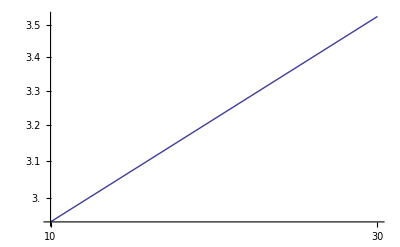
Show[{ListLogLogPlot[InvASDvFreqData],-Graphics-},PlotLabel→Behaviour of 1/(h̃) vs. f^(1/6) explaining why D_Lgrows as f increases,ImageSize→500]

```mathematica
Show[{ListLogLogPlot[InvASDvFreqData],LogLogPlot[2 f^(1/6),{f,10,30}]},PlotLabel->"Behaviour of 1/(h̃) vs. f^(1/6) explaining why D_Lgrows as f increases",ImageSize->500]
```

```mathematica
DLplot=Show[{ListLogLogPlot[DistvFreqData],LogLogPlot[40,{x,GWfreqData[[1]],Last[GWfreqData]},PlotStyle->Red]},PlotLabel->"Maximum luminosity distance assuming Plot 1's frequencies and strains",Frame->True,FrameLabel->{"GW frequency (Hz)","Luminosity Distance (Mpc)"},ImageSize->600]
```

ListLogLogPlot::lpn: DistvFreqData is not a list of numbers or pairs of numbers.

Part::partd: Part specification GWfreqData ⟦ 1 ⟧ is longer than depth of object.

Last::normal: Nonatomic expression expected at position 1 in Last[GWfreqData].

LogLogPlot::llplim: Range specification {x, GWfreqData ⟦ 1 ⟧, Last[GWfreqData]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in Show[{ListLogLogPlot[DistvFreqData], LogLogPlot[40, {x, GWfreqData ⟦ 1 ⟧, Last[GWfreqData]}, PlotStyle → Red]}, PlotLabel → "Maximum luminosity distance assuming Plot 1's frequencies and strains", Frame → True, FrameLabel → {"GW frequency (Hz)", "Luminosity Distance (Mpc)"}, ImageSize → 600].

Show[{ListLogLogPlot[DistvFreqData],LogLogPlot[40,{x,GWfreqData⟦1⟧,Last[GWfreqData]},PlotStyle→Red]},PlotLabel→Maximum luminosity distance assuming Plot 1's frequencies and strains,Frame→True,FrameLabel→{GW frequency (Hz),Luminosity Distance (Mpc)},ImageSize→600]

```mathematica
Orbitsplot=ListPlot[NvsFreq,PlotLabel->"Number of orbits starting from Plot 1's data",AxesLabel->{"Initial GW frequency (Hz)","Number of orbits"},ImageSize->600]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{},PlotLabel→Number of orbits starting from Plot 1's data,AxesLabel→{Initial GW frequency (Hz),Number of orbits},ImageSize→600]

```mathematica
InspiralTimePlot=ListLogLogPlot[TimesVsFreq,PlotLabel->"Time spent in LIGO band assuming starting from Plot 1's data",AxesLabel->{"Initial GW frequency (Hz)","Inspiral time (seconds)"},ImageSize->700]
```

ListLogLogPlot::argx: ListLogLogPlot called with 0 arguments; 1 argument is expected.

ListLogLogPlot[{},PlotLabel→Time spent in LIGO band assuming starting from Plot 1's data,AxesLabel→{Initial GW frequency (Hz),Inspiral time (seconds)},ImageSize→700]

```mathematica
Export["Inspiral_times.pdf",InspiralTimePlot]
Export["number_of_orbits.pdf",Orbitsplot]
Export["luminosity_distances.pdf",DLplot]
Export["ASD_plot.pdf",ASDplot]
```

Inspiral_times.pdf

number_of_orbits.pdf

luminosity_distances.pdf

ASD_plot.pdf

```mathematica
2*10^24*6*10^30*6.67*10^-11/((1.5*10^11)^2)
```

3.55733×10^22

```mathematica
2*10^30*6.67*10^-11/((1.5*10^11)^2)
```

0.00592889

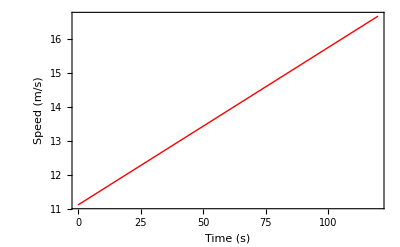

```mathematica
Q1=Plot[0.04633x+11.11,{x,0,120},Frame->True,FrameLabel->{"Time (s)", "Speed (m/s)"},PlotStyle->{Thick,Red}]
```

```mathematica
Export["Q1plot.pdf",Q1]
```

Q1plot.pdf

```mathematica
11.2*10.1
```

113.12

```mathematica
11.2*9.8
```

109.76

```mathematica
583*9.8
```

5713.4

```mathematica
%-643
```

5070.4

```mathematica
D[D[DiracDelta[ϕ-Ω t],ϕ],t]
```

-Ω DiracDelta''[ϕ-t Ω]

```mathematica
Integrate[D[DiracDelta[ϕ-3],ϕ]Exp[-I m ϕ],{ϕ,0,2π}]
Integrate[D[DiracDelta[ϕ-3],{ϕ,2}]Exp[-I m ϕ],{ϕ,0,2π}]
Integrate[D[DiracDelta[ϕ-3],{ϕ,3}]Exp[-I m ϕ],{ϕ,0,2π}]
```

ⅈ ⅇ^(-3 ⅈ m) m

-ⅇ^(-3 ⅈ m) m^2

-ⅈ ⅇ^(-3 ⅈ m) m^3

```mathematica
88/√2.
```

62.2254

```mathematica
Simplify[Integrate[Exp[I(x-3)t],{t,-∞,∞}],Assumptions->x∈Reals]
```

Integrate::idiv: Integral of ⅇ^ⅈ\ t\ (-3 + x) does not converge on {-∞, ∞}.

0

```mathematica
Sin[40./180 Pi]
```

0.642788

```mathematica
%/0.8
```

0.803485

```mathematica
ASDdata=data[[choice,1]];
GWfreqData=data[[choice,2]];
InvASDdata=10^-22/ASDdata;
Strain=(1.`20)ASDdata/(2 √GWfreqData);
(*ASDvFreqData=Table[{GWfreqData[[i]],ASDdata[[i]]},{i,1,Length[GWfreqData]}];*)
InvASDvFreqData=Table[{GWfreqData[[i]],InvASDdata[[i]]},{i,1,Length[GWfreqData]}];
StrainvFreqData=Table[{GWfreqData[[i]],Strain[[i]]},{i,1,Length[GWfreqData]}];
```

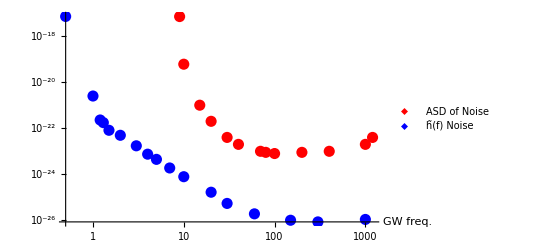

```mathematica
ListLogLogPlot[{ASDvFreqData[[1]],StrainvFreqData},PlotStyle->{{Red,PointSize[0.02]},{Blue,PointSize[0.02]}},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"ASD of Noise","h̃(f) Noise"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]]
```

### Luminosity Distances assuming SNR = 1, and initial frequency given above (units of Mpc, assuming M = m_1+ m_2 = 2.8 M_sun)

```mathematica
LumDist=10^-22/ASDData(0.01/2)^(2/3)GWFreqs^(1/6)*100(* Approximate Blanchet formula *)
```

{{0.0000602452,0.00715312,0.459193,2.40873,12.8857,27.0371,59.3603,67.4402,78.7451,78.5674,79.3701,46.2328,23.8296},{0.000394159,0.00404417,0.421716,1.33442,2.14594,5.52188,9.07886,20.4998,51.5427,90.1236,144.637,235.702,302.617,264.567,113.57,31.7728},{0.00002605,0.0584804,0.602847,0.763679,1.56422,2.34436,5.8526,12.2801,19.1181,40.4417,85.8374,321.164,859.044,1928.49,2696.01,2521.81,1320.94}}

```mathematica
(* Checking the detector strain from the above Subscript[D, L]'s *)
```

```mathematica
H=10^-22 (0.01 GWFreqs/2)^(2/3)100/LumDist
Strain
```

{{2.1×10^-17,1.89737×10^-19,3.87298×10^-21,8.94427×10^-22,2.19089×10^-22,1.26491×10^-22,8.3666×10^-23,8.04984×10^-23,8.×10^-23,1.27279×10^-22,2.×10^-22,6.32456×10^-22,1.38564×10^-21},{2.44949×10^-18,2.64575×10^-19,3.×10^-21,9.96634×10^-22,6.32456×10^-22,2.75855×10^-22,1.87083×10^-22,1.05095×10^-22,5.47723×10^-23,3.79473×10^-23,3.09839×10^-23,4.24264×10^-23,4.33013×10^-23,6.×10^-23,2.4×10^-22,1.03923×10^-21},{7.07107×10^-18,5.×10^-21,5.47723×10^-22,4.5607×10^-22,2.44949×10^-22,1.9799×10^-22,1.03923×10^-22,6.×10^-23,4.47214×10^-23,2.64575×10^-23,1.58114×10^-23,6.7082×10^-24,3.28634×10^-24,2.32379×10^-24,3.06186×10^-24,5.19615×10^-24,2.21359×10^-23}}

{7.07107×10^-18,2.5×10^-21,2.28218×10^-22,1.75412×10^-22,8.16497×10^-23,4.9497474683058326708×10^-23,1.7320508075688772935×10^-23,7.5×10^-24,4.4721359549995793928×10^-24,1.8898223650461361361×10^-24,7.90569×10^-25,1.67705×10^-25,5.47723×10^-26,1.93649×10^-26,1.02062×10^-26,8.66025×10^-27,1.1068×10^-26}

```mathematica
DistvFreqData=Table[{GWFreqs[[j,i]],LumDist[[j,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}]
```

{{{9,0.0000602452},{10,0.00715312},{15,0.459193},{20,2.40873},{30,12.8857},{40,27.0371},{70,59.3603},{80,67.4402},{100,78.7451},{200,78.5674},{400,79.3701},{1000,46.2328},{1200,23.8296}},{{6,0.000394159},{7,0.00404417},{9,0.421716},{9.7,1.33442},{10,2.14594},{11.89,5.52188},{14,9.07886},{20,20.4998},{30,51.5427},{40,90.1236},{60,144.637},{200,235.702},{300,302.617},{400,264.567},{900,113.57},{1200,31.7728}},{{0.5,0.00002605},{1,0.0584804},{1.2,0.602847},{1.3,0.763679},{1.5,1.56422},{2,2.34436},{3,5.8526},{4,12.2801},{5,19.1181},{7,40.4417},{10,85.8374},{20,321.164},{30,859.044},{60,1928.49},{150,2696.01},{300,2521.81},{1000,1320.94}}}

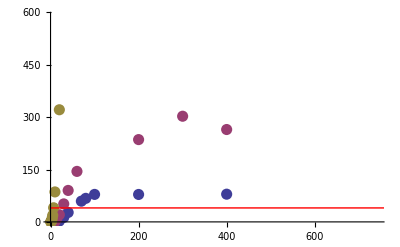

```mathematica
Show[{ListPlot[DistvFreqData,PlotStyle->PointSize[0.02]],Plot[40,{x,GWfreqData[[1]],Last[GWfreqData]},PlotStyle->Red]}]
```